## What happens when you only consider the inequalities in the null that are generated by the full atoms ?

```mathematica
allGraphs2=allGraphs;
```

```mathematica
exps=Simplify[Fold[And,Table[allGraphs2[k,"comp"][allGraphs2[k,"colofourrealnull"],0],{k,atomKeys}]]]
```

2 n123x4+2 n124x3+n12x34+2 n134x2+n13x24+n14x23+2 n1x234+n1x2x3x4≥6 n1234+n12x3x4+n13x2x4+n14x2x3+n1x23x4+n1x24x3+n1x2x34&&2 n1234+n1x2x34>n12x34+n134x2+n1x234&&2 n1234+n1x24x3≥n124x3+n13x24+n1x234&&2 n1234+n1x23x4>n123x4+n14x23+n1x234&&n1x234>n1234&&2 n1234+n14x2x3>n124x3+n134x2+n14x23&&n14x23>n1234&&2 n1234+n13x2x4≥n123x4+n134x2+n13x24&&n13x24≥n1234&&n134x2>n1234&&2 n1234+n12x3x4>n123x4+n124x3+n12x34&&n12x34>n1234&&n124x3>n1234&&n123x4>n1234&&n1234>0

```mathematica
Length[exps]
```

15

```mathematica
Length[DeleteDuplicates[ListofVars[exps]]]
```

15

```mathematica
ExpressionToTable[exps]
```

n1234>0
n1x234>n1234
n123x4>n1234
n134x2>n1234
n124x3>n1234
n14x23>n1234
n13x24≥n1234
n12x34>n1234
2 n1234+n1x23x4>n123x4+n14x23+n1x234
2 n1234+n1x2x34>n12x34+n134x2+n1x234
2 n1234+n1x24x3≥n124x3+n13x24+n1x234
2 n1234+n14x2x3>n124x3+n134x2+n14x23
2 n1234+n13x2x4≥n123x4+n134x2+n13x24
2 n1234+n12x3x4>n123x4+n124x3+n12x34
2 n123x4+2 n124x3+n12x34+2 n134x2+n13x24+n14x23+2 n1x234+n1x2x3x4≥6 n1234+n12x3x4+n13x2x4+n14x2x3+n1x23x4+n1x24x3+n1x2x34

## What happens when you only consider the inequalities in the null that are generated by the fake null atoms ?

```mathematica
exps3=Simplify[Fold[And,Table[allGraphs2[k,"comp"][allGraphs2[k,"colofourrealnull"],0],{k,Keys[allGraphs2]}]]];
```

```mathematica
Length[exps3]
```

127

```mathematica
Length[DeleteDuplicates[ListofVars[exps3]]]
```

15

```mathematica
ExpressionToTable[exps3]
```

n1x234>0
n1234>0
n14x2x3>0
n13x2x4>0
n1x2x3x4>0
n1x23x4>0
n12x3x4>0
n123x4>0
n134x2>0
n1x24x3>0
n124x3>0
n14x23>0
n13x24>0
n1x2x34>0
n12x34>0
n1x234>n1234
n1x23x4>n1x234
n123x4>n1234
n134x2>n1234
n1x24x3>n1x234
n124x3>n1234
n14x23>n1234
n13x24≥n1234
n1x2x34>n1x234
n12x34>n1234
n1x2x3x4>n14x2x3
n14x2x3>n134x2
n14x2x3>n124x3
n14x2x3>n14x23
n1x2x3x4>n13x2x4
n13x2x4>n123x4
n13x2x4>n134x2
n13x2x4>n13x24
n1x2x3x4>n1x23x4
n1x2x3x4>n12x3x4
n1x23x4>n123x4
n12x3x4>n123x4
n1x2x3x4>n1x24x3
n12x3x4>n124x3
n1x23x4>n14x23
n1x2x3x4>n1x2x34
n12x3x4>n12x34
n1x2x34>n134x2
n1x24x3>n124x3
n1x24x3>n13x24
n1x2x34>n12x34
n1234+n1x23x4>n123x4+n1x234
n1234+n1x23x4>n14x23+n1x234
n1234+n1x2x34>n134x2+n1x234
n1234+n1x24x3>n124x3+n1x234
n1234+n1x24x3>n13x24+n1x234
n1234+n1x2x34>n12x34+n1x234
n1234+n14x2x3>n124x3+n134x2
n1234+n14x2x3>n134x2+n14x23
n1234+n14x2x3>n124x3+n14x23
n1234+n13x2x4>n123x4+n134x2
n1234+n13x2x4>n123x4+n13x24
n1234+n13x2x4>n134x2+n13x24
n1x234+n1x2x3x4>n1x23x4+n1x24x3
n1234+n12x3x4>n123x4+n124x3
n1234+n1x23x4>n123x4+n14x23
n1x234+n1x2x3x4>n1x23x4+n1x2x34
n1234+n12x3x4>n123x4+n12x34
n1x234+n1x2x3x4>n1x24x3+n1x2x34
n1234+n12x3x4>n124x3+n12x34
n1234+n1x2x34>n12x34+n134x2
n1234+n1x24x3>n124x3+n13x24
n134x2+n1x2x3x4>n13x2x4+n14x2x3
n124x3+n1x2x3x4>n12x3x4+n14x2x3
n14x23+n1x2x3x4>n14x2x3+n1x23x4
n134x2+n1x2x3x4>n14x2x3+n1x2x34
n124x3+n1x2x3x4>n14x2x3+n1x24x3
n123x4+n1x2x3x4>n13x2x4+n1x23x4
n123x4+n1x2x3x4>n12x3x4+n13x2x4
n134x2+n1x2x3x4>n13x2x4+n1x2x34
n13x24+n1x2x3x4>n13x2x4+n1x24x3
n123x4+n1x2x3x4>n12x3x4+n1x23x4
n124x3+n1x2x3x4>n12x3x4+n1x24x3
n12x34+n1x2x3x4>n12x3x4+n1x2x34
2 n1234+n1x23x4>n123x4+n14x23+n1x234
2 n1234+n1x2x34>n12x34+n134x2+n1x234
2 n1234+n1x24x3≥n124x3+n13x24+n1x234
2 n1234+n14x2x3>n124x3+n134x2+n14x23
2 n1234+n13x2x4≥n123x4+n134x2+n13x24
2 n1x234+n1x2x3x4>n1x23x4+n1x24x3+n1x2x34
2 n1234+n12x3x4>n123x4+n124x3+n12x34
2 n134x2+n1x2x3x4>n13x2x4+n14x2x3+n1x2x34
2 n124x3+n1x2x3x4>n12x3x4+n14x2x3+n1x24x3
2 n123x4+n1x2x3x4>n12x3x4+n13x2x4+n1x23x4
n134x2+n14x23+n1x234+n1x2x3x4>n1234+n14x2x3+n1x23x4+n1x2x34
n124x3+n14x23+n1x234+n1x2x3x4>n1234+n14x2x3+n1x23x4+n1x24x3
n124x3+n134x2+n1x234+n1x2x3x4>n1234+n14x2x3+n1x24x3+n1x2x34
n123x4+n134x2+n1x234+n1x2x3x4>n1234+n13x2x4+n1x23x4+n1x2x34
n123x4+n13x24+n1x234+n1x2x3x4>n1234+n13x2x4+n1x23x4+n1x24x3
n134x2+n13x24+n1x234+n1x2x3x4>n1234+n13x2x4+n1x24x3+n1x2x34
n123x4+n124x3+n1x234+n1x2x3x4>n1234+n12x3x4+n1x23x4+n1x24x3
n123x4+n12x34+n1x234+n1x2x3x4>n1234+n12x3x4+n1x23x4+n1x2x34
n124x3+n12x34+n1x234+n1x2x3x4>n1234+n12x3x4+n1x24x3+n1x2x34
n123x4+n124x3+n134x2+n1x2x3x4>n1234+n12x3x4+n13x2x4+n14x2x3
n123x4+n134x2+n14x23+n1x2x3x4>n1234+n13x2x4+n14x2x3+n1x23x4
n124x3+n134x2+n13x24+n1x2x3x4>n1234+n13x2x4+n14x2x3+n1x24x3
n123x4+n124x3+n14x23+n1x2x3x4>n1234+n12x3x4+n14x2x3+n1x23x4
n124x3+n12x34+n134x2+n1x2x3x4>n1234+n12x3x4+n14x2x3+n1x2x34
n123x4+n12x34+n134x2+n1x2x3x4>n1234+n12x3x4+n13x2x4+n1x2x34
n123x4+n124x3+n13x24+n1x2x3x4>n1234+n12x3x4+n13x2x4+n1x24x3
n123x4+2 n134x2+n14x23+n1x234+n1x2x3x4>2 n1234+n13x2x4+n14x2x3+n1x23x4+n1x2x34
n124x3+2 n134x2+n13x24+n1x234+n1x2x3x4>2 n1234+n13x2x4+n14x2x3+n1x24x3+n1x2x34
n123x4+2 n124x3+n14x23+n1x234+n1x2x3x4>2 n1234+n12x3x4+n14x2x3+n1x23x4+n1x24x3
n124x3+n134x2+n14x23+2 n1x234+n1x2x3x4>2 n1234+n14x2x3+n1x23x4+n1x24x3+n1x2x34
2 n124x3+n12x34+n134x2+n1x234+n1x2x3x4>2 n1234+n12x3x4+n14x2x3+n1x24x3+n1x2x34
2 n123x4+n12x34+n134x2+n1x234+n1x2x3x4>2 n1234+n12x3x4+n13x2x4+n1x23x4+n1x2x34
2 n123x4+n124x3+n13x24+n1x234+n1x2x3x4>2 n1234+n12x3x4+n13x2x4+n1x23x4+n1x24x3
n123x4+n134x2+n13x24+2 n1x234+n1x2x3x4>2 n1234+n13x2x4+n1x23x4+n1x24x3+n1x2x34
n123x4+n124x3+n12x34+2 n1x234+n1x2x3x4>2 n1234+n12x3x4+n1x23x4+n1x24x3+n1x2x34
2 n123x4+n124x3+n134x2+n14x23+n1x2x3x4>2 n1234+n12x3x4+n13x2x4+n14x2x3+n1x23x4
n123x4+2 n124x3+n134x2+n13x24+n1x2x3x4>2 n1234+n12x3x4+n13x2x4+n14x2x3+n1x24x3
n123x4+n124x3+n12x34+2 n134x2+n1x2x3x4>2 n1234+n12x3x4+n13x2x4+n14x2x3+n1x2x34
n123x4+n124x3+n134x2+n13x24+n14x23+n1x234+n1x2x3x4>3 n1234+n13x2x4+n14x2x3+n1x23x4+n1x24x3
n123x4+n124x3+n12x34+n134x2+n14x23+n1x234+n1x2x3x4>3 n1234+n12x3x4+n14x2x3+n1x23x4+n1x2x34
n123x4+n124x3+n12x34+n134x2+n13x24+n1x234+n1x2x3x4>3 n1234+n12x3x4+n13x2x4+n1x24x3+n1x2x34
2 n123x4+2 n124x3+n134x2+n13x24+n14x23+n1x234+n1x2x3x4>4 n1234+n12x3x4+n13x2x4+n14x2x3+n1x23x4+n1x24x3
2 n123x4+n124x3+n12x34+2 n134x2+n14x23+n1x234+n1x2x3x4>4 n1234+n12x3x4+n13x2x4+n14x2x3+n1x23x4+n1x2x34
n123x4+n124x3+2 n134x2+n13x24+n14x23+2 n1x234+n1x2x3x4>4 n1234+n13x2x4+n14x2x3+n1x23x4+n1x24x3+n1x2x34
n123x4+2 n124x3+n12x34+2 n134x2+n13x24+n1x234+n1x2x3x4>4 n1234+n12x3x4+n13x2x4+n14x2x3+n1x24x3+n1x2x34
n123x4+2 n124x3+n12x34+n134x2+n14x23+2 n1x234+n1x2x3x4>4 n1234+n12x3x4+n14x2x3+n1x23x4+n1x24x3+n1x2x34
2 n123x4+n124x3+n12x34+n134x2+n13x24+2 n1x234+n1x2x3x4>4 n1234+n12x3x4+n13x2x4+n1x23x4+n1x24x3+n1x2x34
2 n123x4+2 n124x3+n12x34+2 n134x2+n13x24+n14x23+2 n1x234+n1x2x3x4≥6 n1234+n12x3x4+n13x2x4+n14x2x3+n1x23x4+n1x24x3+n1x2x34

## What happens when you only consider the inequalities in the null that are generate by all graphs ?

```mathematica
Select[Keys[allGraphs],IsomorphicGraphQ[allGraphs[#,"graph"],CompleteGraph[4]]&]
```

{364}

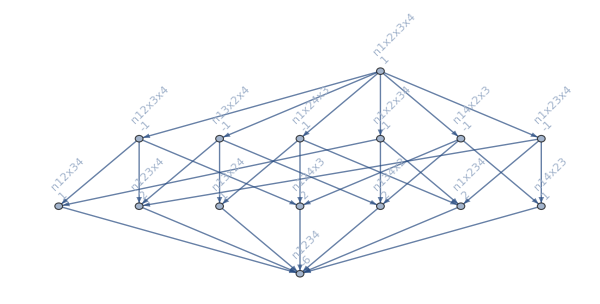

```mathematica
MobiusGraph[364]
```

```mathematica
n123x4+n124x3+n13x24+n1x2x3x4>n1234+n12x3x4+n13x2x4+n1x24x3
```